Standardize NIG PDF’s by setting location and scale

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=(α^2-β^2)^(3/2)/α^2 
μs[α_,β_]:=-(δs[α,β] β)/(√(α^2-β^2))
```

```mathematica
Correlations[n_,α_,β_,δ_]:=Module[{μ,μ1,μ2,δ1,δ2,γ,μIG,μ1IG,μ2IG,λ,λ1,λ2,Y,W,W1,W2,Z,Z1,Z2,X1,X2},
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μ=0;
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
SeedRandom[12345];
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
{δ/δs[α,β],Correlation[X1,X2],(6 ArcSin[δ/(2 δs[α,β])])/π,(*(6 ArcSin[1/2 Correlation[X1,X2]])/π,*)SpearmanRho[X1,X2]}
]
```

```mathematica
sol=Solve[δ/δs[α,α-1]==0.2,δ]
```

{{δ→(0.2 (α^2-0.81)^(3/2))/α^2}}

```mathematica
r=Table[Correlations[200000, α, α-1, δ/.sol⟦1⟧], {α,1,20}];
```

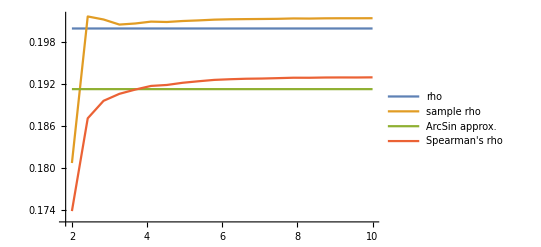

```mathematica
ListPlot[rᵀ,Joined->True,DataRange->{2,10},PlotLegends->{"rho", "sample rho", "ArcSin approx.", "Spearman's rho"}]
```